```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\BS.m"
```

```mathematica
TotalImpliedVol[α_,κ_,ρ_,σ_,f1_,f2_,f3_,f4_,g1_,g2_,k_,T_]:=Module[{z,σ0,σ1,σ2,σ3,σ4},
z=(k-1)/(σ √T);
σ0=σ;
σ1=(z σ)/(2 √T)((f1-1)σ T+√8 g1 α ρ(κ T +ⅇ^(-κ T)-1)/(κ^(3/2)T));
σ2=(σ ⅇ^(-2κ T))/(24 T^3 κ^3)(12 √2 ⅇ^(T κ)f1 g1 α κ^(3/2)(ⅇ^(T κ)(T κ-1)+1)ρ σ T^2-
κ T (ⅇ^(2κ T)(f1^2-2f2-1)T^3 κ^2 σ^2
-6g2 α^2(2 ⅇ^(2T κ)T^2 κ^2-5 ⅇ^(2T κ)T κ+T κ-8 ⅇ^(T κ)+6 ⅇ^(2T κ)+2)ρ^2)
-6g1 α^2(2 ⅇ^(2T κ)T^3(ρ^2-1)κ^3+T^2(-9 ⅇ^(2T κ)ρ^2+ρ^2+5 ⅇ^(2T κ)-1)κ^2
-2(ⅇ^(T κ)-1)T(-7 ⅇ^(T κ)ρ^2+ρ^2+3 ⅇ^(T κ)-1)κ-4(ⅇ^(T κ)-1)ρ^2)
+z^2(-12 √2 ⅇ^(T κ)g1 α κ^(3/2)(ⅇ^(T κ)(T κ -1)+1)ρ σ T^2
-κ T (ⅇ^(2T κ)(2 f1^2+6f1-4f2-8)T^3 κ^2 σ^2
-6g2 α^2(4 ⅇ^(2T κ)T κ+8 ⅇ^(T κ)-6 ⅇ^(2T κ)-2)ρ^2)
-6 g1^2 α^2(T^2(12 ⅇ^(2T κ)ρ^2-4 ⅇ^(2T κ))κ^2+8(ⅇ^(T κ)-1)^2 ρ^2
-2(ⅇ^(T κ)-1)T(11 ⅇ^(T κ)ρ^2-ρ^2-3 ⅇ^(T κ)+1)κ)));
σ3=(T^(3/2)z σ^4)/48(-f1^3+f1^2+(2f2+3)f1-2f2+2f3-3
+2 z^2(f1^3+f1^2+(4-2f2)f1-2f2+f3-6));
σ4=(-T^2 σ^5)/5760(8 z^4(19 f1^4+15 f1^3+(20-46f2)f1^2+6(3f3-5f2+15)f1
-40f2+(16 f2^2+15f3)-6f4-144)
-2 z^2(11 f1^4+30 f1^3+(20-44f2)f1^2+6(12f3-10f2-45)f1
+140f2+(44 f2^2-60f3)+36f4+209)
-3(3 f1^4-2(6f2+5)f1^2+16f3 f1-8 f2^2+20f2+8f4+7));σ0+σ1+σ2+σ3+σ4]
```

```mathematica
HypHypImpliedVolTotalImpliedVol[α_,κ_,ρ_,σ_,β_,k_,T_]:=Module[{f1=β,f2=β(β-1),f3=-3β(β-1),f4=-3β(β-1)(β^2-4),g1=1,g2=1},
TotalImpliedVol[α,κ,ρ,σ,f1,f2,f3,f4,g1,g2,k,T]]
```

```mathematica
HypHypDelta[α_,κ_,ρ_,σ_,β_,k_,T_]:=Module[{shift=Min[Abs[k]/100,0.0001]},
(-BS[1,k+shift,T,HypHypImpliedVolTotalImpliedVol[α,κ,ρ,σ,β,k+shift,T]]+BS[1,k-shift,T,HypHypImpliedVolTotalImpliedVol[α,κ,ρ,σ,β,k-shift,T]])/(2shift)]
```

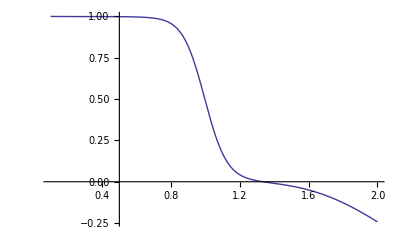

```mathematica
Module[{α=3/5,κ=1/5,ρ=0.,σ=0.05,β=.5,T=5},Plot[HypHypDelta[α,κ,ρ,σ,β,k,T],{k,0.1,2}]]
```

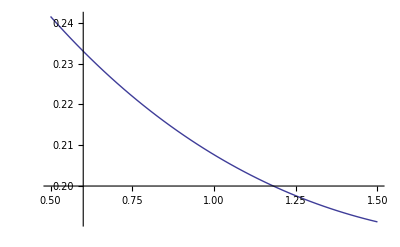

```mathematica
Module[{α=0.4,κ=0.5,ρ=-0.3,σ=0.2,β=.7,T=10},Plot[HypHypImpliedVolTotalImpliedVol[α,κ,ρ,σ,β,k,T],{k,0.5,1.5}]]
```

```mathematica
Module[{α=0.4,κ=0.5,ρ=-0.3,σ=0.2,β=.7,T=10},(HypHypImpliedVolTotalImpliedVol[α,κ,ρ,σ,β,#,T])& /@ Table[0.5+i/10,{i,0,10}]]
```

{0.241526,0.233006,0.225437,0.218738,0.212838,0.207672,0.203185,0.199331,0.19607,0.193373,0.191218}

```mathematica
Module[{α=3/5,κ=1,ρ=-0.5,σ=0.1,β=0.7},Plot3D[HypHypImpliedVolTotalImpliedVol[α,κ,ρ,σ,β,k,T],{k,0.1,2},{T,1,10}]]
```

-Graphics3D-

```mathematica
HypHypImpliedVolTotalImpliedVol[α_,κ_,ρ_,σ_,β_,k_,T_]
```

```mathematica
CForm[HypHypImpliedVolTotalImpliedVol[alpha,kappa,rho,sigma,beta,k,T]]
```

sigma + ((-1 + k)*Power(sigma,3)*(-3 - 8*(-1 + beta)*beta + Power(beta,2) - Power(beta,3) + beta*(3 + 2*(-1 + beta)*beta) + 
        (2*(-6 - 5*(-1 + beta)*beta + Power(beta,2) + Power(beta,3) + beta*(4 - 2*(-1 + beta)*beta))*Power(-1 + k,2))/
         (Power(sigma,2)*T))*T)/48. - (Power(sigma,5)*
      (-3*(7 + 20*(-1 + beta)*beta - 48*(-1 + beta)*Power(beta,2) - 8*Power(-1 + beta,2)*Power(beta,2) + 3*Power(beta,4) - 
           2*Power(beta,2)*(5 + 6*(-1 + beta)*beta) - 24*(-1 + beta)*beta*(-4 + Power(beta,2))) + 
        (8*(-144 - 85*(-1 + beta)*beta + 16*Power(-1 + beta,2)*Power(beta,2) + 15*Power(beta,3) + 19*Power(beta,4) + 
             Power(beta,2)*(20 - 46*(-1 + beta)*beta) + 6*beta*(15 - 14*(-1 + beta)*beta) + 18*(-1 + beta)*beta*(-4 + Power(beta,2))
             )*Power(-1 + k,4))/(Power(sigma,4)*Power(T,2)) - 
        (2*(209 + 320*(-1 + beta)*beta + 44*Power(-1 + beta,2)*Power(beta,2) + 30*Power(beta,3) + 11*Power(beta,4) + 
             6*beta*(-45 - 46*(-1 + beta)*beta) + Power(beta,2)*(20 - 44*(-1 + beta)*beta) - 
             108*(-1 + beta)*beta*(-4 + Power(beta,2)))*Power(-1 + k,2))/(Power(sigma,2)*T))*Power(T,2))/5760. + 
   ((-1 + k)*((-1 + beta)*sigma*T + (2*Sqrt(2)*alpha*rho*(-1 + Power(E,-(kappa*T)) + kappa*T))/(Power(kappa,1.5)*T)))/(2.*T) + 
   (sigma*(-6*Power(alpha,2)*(-4*(-1 + Power(E,kappa*T))*Power(rho,2) - 
           2*(-1 + Power(E,kappa*T))*kappa*(-1 + 3*Power(E,kappa*T) + Power(rho,2) - 7*Power(E,kappa*T)*Power(rho,2))*T + 
           Power(kappa,2)*(-1 + 5*Power(E,2*kappa*T) + Power(rho,2) - 9*Power(E,2*kappa*T)*Power(rho,2))*Power(T,2) + 
           2*Power(E,2*kappa*T)*Power(kappa,3)*(-1 + Power(rho,2))*Power(T,3)) + 
        12*Sqrt(2)*alpha*beta*Power(E,kappa*T)*Power(kappa,1.5)*rho*sigma*Power(T,2)*(1 + Power(E,kappa*T)*(-1 + kappa*T)) - 
        kappa*T*((-1 - 2*(-1 + beta)*beta + Power(beta,2))*Power(E,2*kappa*T)*Power(kappa,2)*Power(sigma,2)*Power(T,3) - 
           6*Power(alpha,2)*Power(rho,2)*(2 - 8*Power(E,kappa*T) + 6*Power(E,2*kappa*T) + kappa*T - 5*Power(E,2*kappa*T)*kappa*T + 
              2*Power(E,2*kappa*T)*Power(kappa,2)*Power(T,2))) + 
        (Power(-1 + k,2)*(-6*Power(alpha,2)*(8*Power(-1 + Power(E,kappa*T),2)*Power(rho,2) - 
                2*(-1 + Power(E,kappa*T))*kappa*(1 - 3*Power(E,kappa*T) - Power(rho,2) + 11*Power(E,kappa*T)*Power(rho,2))*T + 
                Power(kappa,2)*(-4*Power(E,2*kappa*T) + 12*Power(E,2*kappa*T)*Power(rho,2))*Power(T,2)) - 
             12*Sqrt(2)*alpha*Power(E,kappa*T)*Power(kappa,1.5)*rho*sigma*Power(T,2)*(1 + Power(E,kappa*T)*(-1 + kappa*T)) - 
             kappa*T*((-8 + 6*beta - 4*(-1 + beta)*beta + 2*Power(beta,2))*Power(E,2*kappa*T)*Power(kappa,2)*Power(sigma,2)*
                 Power(T,3) - 6*Power(alpha,2)*Power(rho,2)*
                 (-2 + 8*Power(E,kappa*T) - 6*Power(E,2*kappa*T) + 4*Power(E,2*kappa*T)*kappa*T))))/(Power(sigma,2)*T)))/
    (24.*Power(E,2*kappa*T)*Power(kappa,3)*Power(T,3))